## A1: First Order Rate Law

Part A)

```mathematica
Eqn1={
A'[t]==-k A[t],
A[0]==A0
};
(*Note: must add a space after k, or it does not read the equation properly*)
```

```mathematica
Sol1 = DSolve[Eqn1, A[t], t][[1]]
```

{A[t]→A0 ⅇ^(-k t)}

```mathematica
A1[t_]=A[t]/.Sol1
(*Sol1 is in the form of a substitution, not an assignment. This defines a function by using the substitution.*)
```

A0 ⅇ^(-k t)

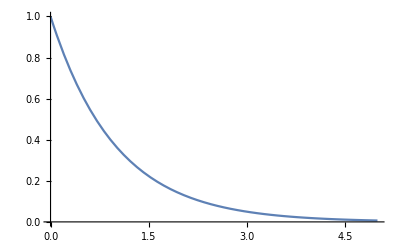

```mathematica
Clear[kSub];
Clear[A0Sub];
kSub=1;
A0Sub=1;
Plot[A1[t]/.{A0->A0Sub,k->kSub},{t,0,5}]
(*Substituting specific values of A0 and k into A1[t] to plot*)
```

```mathematica
Clear[HalfLife];
HalfLife= (Log[2.]/k)/.{k->1kSub}
```

0.693147

Reading coordinates from the graph for the half-life of the reaction, the value we obtain for time t when A=1/2 is approximately t=0.712. On the other hand, using the equation for half life where t=(ln2)/k, gave us a value of 0.693. Although there is a margin of error, these values are reasonably close and indicate that the equation and graph are mostly consistent. 

Below, we are changing the value of k from 1 to 10.

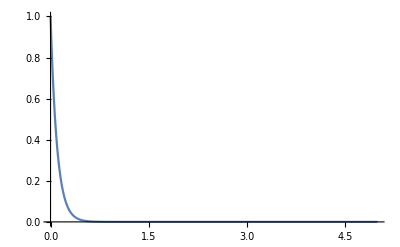

```mathematica
Clear[kSub];
Clear[A0Sub];
kSub = 10;
A0Sub=1;
Plot[A1[t]/.{A0->A0Sub,k->kSub},{t,0,5},PlotRange->{0,1}]
```

```mathematica
Clear[HalfLife];
HalfLife= (Log[2.]/k)/.{k->1kSub}
```

0.0693147

From the graph’s coordinates when A=1/2, we get a half life of approximately t = 0.067, which is close to the half life obtained from the equation. Thus, the change in half life predicted from the equation for the corresponding change in k was also predicted accurately by the plot.

Part B)

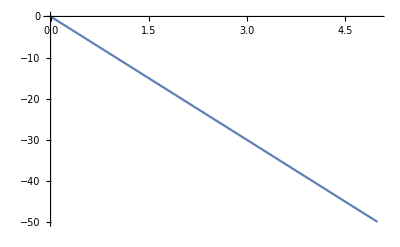

{-10 t}

```mathematica
Clear[kSub];
Clear[A0Sub];
kSub = 10;
A0Sub=1;
Plot[{-k t + Log[A0]}/.{A0->A0Sub,k->kSub},{t,0,5}]
```

From the graph, we can calculate that the slope of the line is about -10 and the y-intercept is presumably 0.
The slope of the graph is consistent with the value of -k, which is negative of the rate constant. The y-intercept is consistent with the value of the natural log of the initial concentration A0.

## A2: Second Order Rate Law

Part A)

```mathematica
Clear[A]
Eqn3={
A'[t]==-k *(A[t])^2,
A[0]==A0
};
Sol2=DSolve[Eqn3,A[t],t][[1]]
```

{A[t]→A0/(1+A0 k t)}

```mathematica
A2[t_]=A[t]/.Sol2
```

A0/(1+A0 k t)

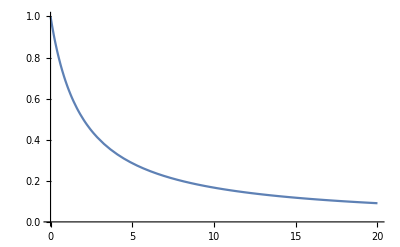

```mathematica
Clear[kSub];
Clear[A0Sub];
kSub=0.5;
A0Sub=1;
Plot[A2[t]/.{A0->A0Sub,k->kSub},{t,0,20}, PlotRange->{0,1}]
```

Part B)

```mathematica
Clear[A0Sub];
A0Sub = 1;
halfLifeeq1 = A2[t]/.{A0->A0Sub,k->kSub}
```

1/(1+0.5 t)

```mathematica
halfLife1 = NSolve[halfLifeeq1==0.5*A0Sub, t][[1]]
```

{t→2.}

```mathematica
Clear[A0Sub];
A0Sub=0.5;
halfLifeeq2 = A2[t]/.{A0->A0Sub,k->kSub}
```

0.5/(1+0.25 t)

```mathematica
halfLife2=NSolve[halfLifeeq2==0.5*A0Sub, t][[1]]
```

{t→4.}

## Part C

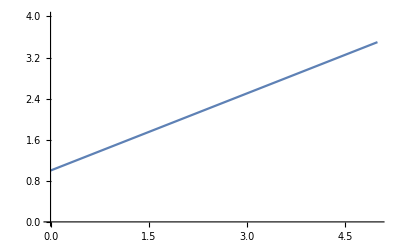

```mathematica
Clear[kSub];
Clear[A0Sub];
kSub = 0.5;
A0Sub=1;
Plot[{k t+(1/A0)}/.{A0->A0Sub,k->kSub},{t,0,5}, PlotRange->{0,4}]
(*need to give a space after k*)
```

From the graph, we can calculate the slope of this line is approximately 0.5 and the y-intercept is approximately 1.
The slope of the line is consistent with the value of the rate constant k, which is 0.5. The intercept of the line is consistent with the value of 1/A0, which is 1.

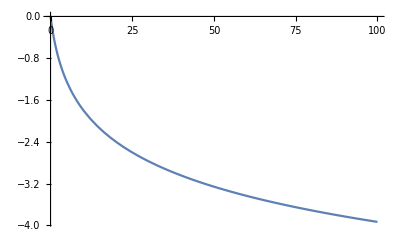

```mathematica
Plot[Log[A0/(k t A0 + 1)]/.{A0->A0Sub,k->kSub},{t,0,100}]
```

As you can see, plotting the natural log of the solution equation does not result in a linear graph, contrary to what we had for the first order reaction.

## A3: Determining Rate Law from Data

Part A)

```mathematica
Clear[rate1data]
rate1data=Import["C:\\Users\\prana\\OneDrive - The University of Texas at Austin\\Desktop\\Spring 2022\\comp chem\\hw\\hw1\\rate1.dat"]
```

{{0,0.4},{1,0.30303},{2,0.243902},{3,0.204082},{4,0.175439},{5,0.153846},{6,0.136986},{7,0.123457},{8,0.11236},{9,0.103093},{10,0.0952381},{11,0.0884956},{12,0.0826446},{13,0.0775194},{14,0.0729927},{15,0.0689655}}

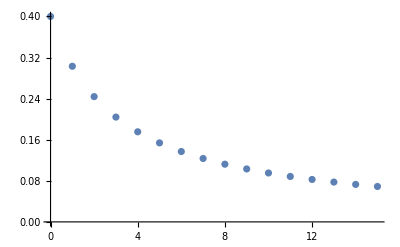

```mathematica
ListPlot[rate1data]
```

Part B)

```mathematica
LogList=ArrayReshape[{0,0,1,0,2,0,3,0,4,0,5,0,6,0,7,0,8,0,9,0,10,0,11,0,12,0,13,0,14,0,15,0},{16,2}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0}}

{{0,-0.916291},{1,-1.19392},{2,-1.41099},{3,-1.58923},{4,-1.74046},{5,-1.8718},{6,-1.98788},{7,-2.09186},{8,-2.18605},{9,-2.27212},{10,-2.35138},{11,-2.4248},{12,-2.49321},{13,-2.55723},{14,-2.6174},{15,-2.67415}}

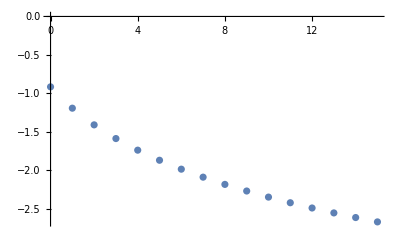

```mathematica
For[i=1,i<=16,i++,
LogList[[i,2]]=Log[rate1data[[i,2]]]
]
LogList
ListPlot[LogList]
```

Plotting the logarithm of the concentration vs. time does not return a straight line. This indicates that the reaction is not first order.

```mathematica
ReciprocalList = ArrayReshape[{0,0,1,0,2,0,3,0,4,0,5,0,6,0,7,0,8,0,9,0,10,0,11,0,12,0,13,0,14,0,15,0},{16,2}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0}}

{{0,2.5},{1,3.3},{2,4.10001},{3,4.89999},{4,5.69999},{5,6.50001},{6,7.30002},{7,8.09999},{8,8.89996},{9,9.69998},{10,10.5},{11,11.3},{12,12.1},{13,12.9},{14,13.7},{15,14.5}}

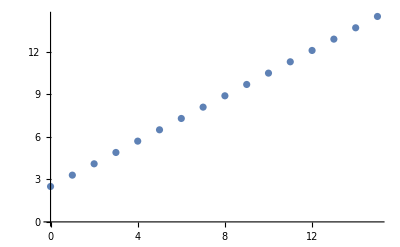

```mathematica
For[i=1,i<=16,i++,
ReciprocalList[[i,2]]=1/(rate1data[[i,2]])
]
ReciprocalList
ListPlot[ReciprocalList]
```

Plotting the reciprocal of the concentration vs. time returns a straight line, which indicates that the reaction is second order.

Part C)

```mathematica
rate2data = Import["C:\\Users\\prana\\OneDrive - The University of Texas at Austin\\Desktop\\Spring 2022\\comp chem\\hw\\hw1\\rate2.dat"]
```

{{0.,0.01},{20.,0.0097},{50.,0.00928},{100.,0.00861},{200.,0.00741},{400.,0.00549},{700.,0.0035},{1000.,0.00223}}

{{0,0},{20,0},{50,0},{100,0},{200,0},{400,0},{700,0},{1000,0}}

{{0,-4.60517},{20,-4.63563},{50,-4.67989},{100,-4.75483},{200,-4.90492},{400,-5.20483},{700,-5.65499},{1000,-6.10575}}

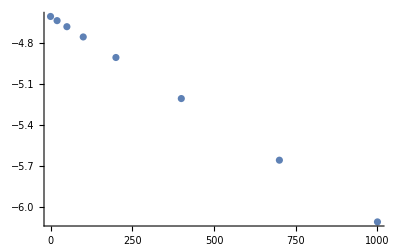

```mathematica
LogList2=ArrayReshape[{0,0,20,0,50,0,100,0,200,0,400,0,700,0,1000,0},{8,2}]
For[i=1,i<=8,i++,
LogList2[[i,2]]=Log[rate2data[[i,2]]]
]
LogList2
ListPlot[LogList2]
```

Plotting the logarithm of concentration vs. time results in a straight line, which indicates that the reaction is first order.

{{0,0},{20,0},{50,0},{100,0},{200,0},{400,0},{700,0},{1000,0}}

{{0,100.},{20,103.093},{50,107.759},{100,116.144},{200,134.953},{400,182.149},{700,285.714},{1000,448.43}}

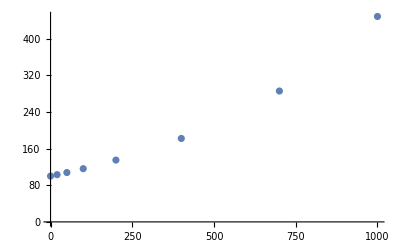

```mathematica
ReciprocalList2=ArrayReshape[{0,0,20,0,50,0,100,0,200,0,400,0,700,0,1000,0},{8,2}]
For[i=1,i<=8,i++,
ReciprocalList2[[i,2]]=1/(rate2data[[i,2]])
]
ReciprocalList2
ListPlot[ReciprocalList2]
```

Plotting the reciprocal of the concentration vs. time does not result in a straight line, which suggests the reaction is not second order.

Part D)

```mathematica
rate1slope = (ReciprocalList[[16,2]]-ReciprocalList[[1,2]])/15
```

0.8

```mathematica
rate1intercept=ReciprocalList[[1,2]]
```

2.5

```mathematica
rate2slope=(LogList2[[8,2]]-LogList2[[1,2]])/1000
```

-0.00150058

```mathematica
rate2intercept=LogList2[[1,2]]
```

-4.60517

```mathematica
rate1line=Fit[ReciprocalList,{1,t},t]
```

2.5+0.8 t

```mathematica
rate2line = Fit[LogList2,{1,t},t]
```

-4.60502-0.00150036 t

Part E)

The rate constant k for the second reaction is the negative of the slope. Thus, k = 0.00150036.

Part F)

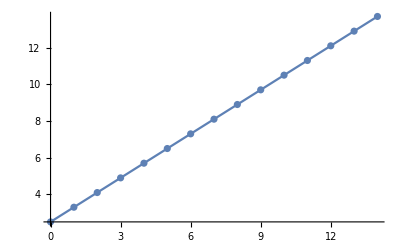

```mathematica
Show[Plot[rate1line,{t,0,14}],ListPlot[ReciprocalList]]
```

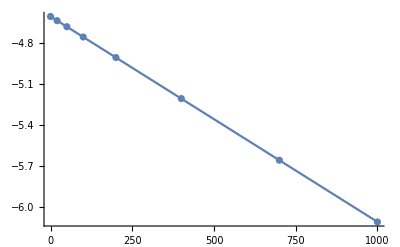

```mathematica
Show[Plot[rate2line,{t,0,1000}],ListPlot[LogList2]]
```

Based on the graphs, the lines seem to be accurately fit to the data with minimal or no error.